```mathematica
<<DoFun`
```

DoFun loaded.

Version 2.0.3
Reinhard Alkofer, Jens Braun, Markus Q. Huber, Kai Schwenzer, 2008-2017

Details on http://physik.uni-graz.at/~mqh/DoFun.

```mathematica
<<ERGE`
```

ERGE package loaded.

Version 0.2.1.

Copyright (C) 2016-2017, Nils Strodthoff.

Using FORM 4.1 (Jan 13 2014) 64-bits.

```mathematica
?doERGE
```

Derives the symbolic flow equation for a given n-point function in a specified theory.
Parameters:
fields: a list of the form {{bosons},{fermions}} which can/ have to contain again sublists of two elements in case of fermionic fields/complex fields. e.g. {{phi}{{psi,psib}}} for a Yukawa theory
interactions: list of interaction terms to be considered (including non-diagonal propagators) permutations are automatically considered e.g. {{phi,phi,phi},{phi,phi,phi,phi},{phi,psi,psib}} for a Yukawa theory with cubic and quartic bosonic interactions.
Derivatives: specifies the npt function for which the flow equation should be derived e.g. {phi,phi} for a bosonic propagator. All derivatives are understood as left derivatives with the rightmost entry acting first unless DoFunInput==True

Options:
DoFunOutput->True/False convert to DoFun-compatible syntax and conventions (op function, vertex definition)
DoFunInput->True/False derivatives in DoFun compatible form (left/right derivatives for afermions/fermions; leftmost derivative acts first)
OffDiagonalRegulators->True/False takes into account off-diagonal regulator terms (i.e. all explicitly specified propagators via interaction terms)
MasterEqn->TrMMA[dtRMMMA,etaMMMA,GMMMA]

```mathematica
?DefineFieldSpecificERGE
```

Prepares ERGE for call of getAEERGE
Parameter:
list of fields (possibly with sublists of two elements for fermions/ complex bosons for DoFun compatibility) where every entry is expected to be of the form field1[mom,index1,...,indexn] e.g. DefineFieldSpecificERGE[{{psi[mom,color],psib[mom,color]},phi[mom,flav]}]

```mathematica
?getAEERGE
```

Returns algebraic expression for a given symbolic expression
Parameters:
symbolic_eq: output of doERGE/doEDSE/doEMAGIC
fieldlist: list matching that of the corresponding call used to create the corresponding symbolic expression; every sublist is expected to be of the form {field,index_in_symbolic_eq,...}, where ... denotes all explicit field indices specified in DefineFieldSpecificERGE for that specific field type.
e.g. getAEERGE[myres,{{psi,i1,p1,a1},{psib,i2,p2,a2}}]

## For Debugging

```mathematica
SetDirectory[NotebookDirectory[]];
DebuggingModeERGE[True]
```

Debugging mode enabled.

## Yukawa Systems

### propagator (Example for getAE)

```mathematica
defineFields[{phi},{{psi,psib}},{}];
actionsymbolic={{phi,phi},{phi,phi,phi},{phi,phi,phi,phi},{psi,psib},{psi,psib,phi},{psi,psib,psi,psib}};
fieldsERGE={{phi},{{psi,psib}}};
interactionsERGE={{phi,phi,phi},{phi,phi,phi,phi},{psib,psi,phi},{psib,psi,psib,psi}};
plotstyle=
{{phi,Red,Dashed},{psi,Black}};
```

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{psi,psib}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^-1= | -Graphics--^ | -Graphics-+^ | -Graphics-+^ |

```mathematica
DefineFieldSpecificERGE[{{psi[mom,color],psib[mom,color]},phi[mom,flav]}]
```

```mathematica
getAEERGE[myres,{{psi,i1,p1,a1},{psib,i2,p2,a2}}]
```

deltam[p1+p2] dR[psib[-p1+q1,color2iint6],psi[p1-q1,color2iint1],explicit→True] P[phi[-q1,flav2iint3],phi[q1,flav2iint4],explicit→True] P[psi[p1-q1,color2iint1],psib[-p1+q1,color2iint2],explicit→True] P[psi[p1-q1,color2iint5],psib[-p1+q1,color2iint6],explicit→True] V[phi[-q1,flav2iint3],psib[-p1+q1,color2iint2],psi[p1,a1],explicit→True] V[phi[q1,flav2iint4],psib[p2,a2],psi[p1-q1,color2iint5],explicit→True]+deltam[p1+p2] dR[phi[p1-q1,flav2iint1],phi[-p1+q1,flav2iint6],explicit→True] P[phi[p1-q1,flav2iint1],phi[-p1+q1,flav2iint2],explicit→True] P[phi[p1-q1,flav2iint5],phi[-p1+q1,flav2iint6],explicit→True] P[psi[q1,color2iint4],psib[-q1,color2iint3],explicit→True] V[phi[p1-q1,flav2iint5],psib[p2,a2],psi[q1,color2iint4],explicit→True] V[phi[-p1+q1,flav2iint2],psib[-q1,color2iint3],psi[p1,a1],explicit→True]-deltam[p1+p2] dR[psib[q1,color2iint4],psi[-q1,color2iint1],explicit→True] P[psi[-q1,color2iint1],psib[q1,color2iint2],explicit→True] P[psi[-q1,color2iint3],psib[q1,color2iint4],explicit→True] V[psib[p2,a2],psib[q1,color2iint2],psi[-q1,color2iint3],psi[p1,a1],explicit→True]

### 4 Fermi interaction

```mathematica
defineFields[{phi},{{psi,psib}},{}];
actionsymbolic={{phi,phi},{phi,phi,phi},{phi,phi,phi,phi},{psi,psib},{psi,psib,phi},{psi,psib,psi,psib}};
fieldsERGE={{phi},{{psi,psib}}};
interactionsERGE={{phi,phi,phi},{phi,phi,phi,phi},{psib,psi,phi},{psib,psi,psib,psi}};
plotstyle=
{{phi,Red,Dashed},{psi,Black}};
```

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{psi,psi,psib,psib}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ |

```mathematica
dofunres=doRGE[actionsymbolic,{psi,psi,psib,psib}];
RGEPlot[dofunres,plotstyle]
```

```mathematica
myres2=doERGE[fieldsERGE,interactionsERGE,{psib,psi},DoFunOutput->False,DoFunInput->False]
```

### RGEPlot issue (assumes a particular order within the vertex)

```mathematica
RGEPlot[-op[dR[{psib,r1},{psi,s1}],P[{psi,t1},{psib,r1}],P[{psi,s1},{psib,v1}],V[{psib,i2},{psib,v1},{psi,t1},{psi,i1}]],{{phi,Black},{psi,Red}}]
RGEPlot[-op[dR[{psib,r1},{psi,s1}],P[{psi,t1},{psib,r1}],P[{psi,s1},{psib,v1}],V[{psib,i2},{psib,v1},{psi,i1},{psi,t1}]],{{phi,Black},{psi,Red}}]
```

-Graphics--^

-Graphics--^

### Yukawa2 checks

```mathematica
defineFields[{phi},{{psi,psib}},{}];
actionsymbolic={{phi,phi},{psi,psib},{psi,psib,phi,phi},{psib,psi,psib,psi}};
fieldsERGE={{phi},{{psi,psib}}};
interactionsERGE={{psib,psi,phi,phi},{psib,psi,psib,psi}};
plotstyle=
{{phi,Red,Dashed},{psi,Black}};
```

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{psib,psib,psi,psi}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ |

```mathematica
myres[[5]]
```

op[P[{psi,iint2},{psib,iint1}],P[{psi,iint3},{psib,iint4}],P[{psi,iint6},{psib,iint5}],dR[{psib,iint1},{psi,iint6}],V[{psib,i1},{psib,i2},{psi,iint2},{psi,iint3}],V[{psib,iint4},{psib,iint5},{psi,i3},{psi,i4}]]

```mathematica
dofunres=doRGE[actionsymbolic,{psib,psib,psi,psi}];
RGEPlot[dofunres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics-+^ | -Graphics-+2^ | -Graphics--2^
 | -Graphics-+^ |  |  |

## YM Theory

```mathematica
defineFields[{A},{},{{Gf,Gb}}];
actionsymbolic={{A,A},{A,A,A},{A,A,A,A},{Gf,Gb},{Gf,Gb,A}};
fieldsERGE={{A},{{Gf,Gb}}};
interactionsERGE={{A,A,A},{A,A,A,A},{Gf,Gb,A}};
plotstyle={{A,Red},{Gf,Black,Dashed}};
```

### Ghost Propagator

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{Gb,Gf}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^-1= | -Graphics-+^ | -Graphics-+^ |  |

```mathematica
dofunres=doRGE[actionsymbolic,{Gb,Gf}];
RGEPlot[dofunres,plotstyle]
```

-Graphics-∂_t ^-1= | -Graphics-+^ | -Graphics-+^ |  |

### Gluon Propagator

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{A,A}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics--^

```mathematica
dofunres=doRGE[actionsymbolic,{A,A}];
RGEPlot[dofunres,plotstyle]
```

-Graphics-∂_t ^-1= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--2^ |

### 3-Gluon Vertex (DoFun identifies ghost loops)

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{A,A,A}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

```mathematica
dofunres=doRGE[actionsymbolic,{A,A,A}];
RGEPlot[dofunres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ |  |  |

### Ghost-Gluon Vertex

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{Gb,Gf,A}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ |  |

```mathematica
dofunres=doRGE[actionsymbolic,{Gb,Gf,A}];
RGEPlot[dofunres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ |  |

### 4-Gluon Vertex

```mathematica
myres=doERGE[fieldsERGE,interactionsERGE,{A,A,A,A}];
RGEPlot[myres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

```mathematica
dofunres=doRGE[actionsymbolic,{A,A,A,A}];
RGEPlot[dofunres,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics-+2^ |  |  |

## Full QCD

```mathematica
defineFields[{A,pion,sigma(*,Amu*)},{{Psi,Psib}},{{Gf,Gb}}];
actionsymbolic={{A,4},{Gf,Gb},{pion,pion},{Psi,Psib},{sigma,sigma},{Gb,Gf,A},{pion,pion,sigma},{Psi,Psib,A},(*{Psi,Psib,Amu},*){Psi,Psib,pion},{Psi,Psib,sigma},{sigma,sigma,sigma},{A,A,Gb,Gf},{A,A,pion,pion},{Gb,Gb,Gf,Gf},{Gb,Gf,Psib,Psi},{Gf,Gb,pion,pion},{pion,pion,pion,pion},{pion,pion,sigma,sigma},{Psi,Psib,pion,pion},{Psi,Psib,sigma,pion},{Psi,Psib,sigma,sigma},{Psib,Psi,A,A},{Psib,Psi,Psib,Psi},{sigma,sigma,sigma,sigma},{pion,pion,pion,pion,sigma},{pion,pion,sigma,sigma,sigma},{Psi,Psib,pion,pion,pion},{Psi,Psib,sigma,pion,pion},{Psi,Psib,sigma,sigma,pion},{Psi,Psib,sigma,sigma,sigma},{Psib,Psi,A,A,A},{pion,pion,pion,pion,pion,pion},{pion,pion,pion,pion,sigma,sigma},{pion,pion,sigma,sigma,sigma,sigma},{Psib,Psi,Psib,Psi,Psib,Psi},{sigma,sigma,sigma,sigma,sigma,sigma}};
interactionsERGE=Join[Delete[actionsymbolic,1],{{A,A,A},{A,A,A,A}}];
fieldsERGE={{A,pion,sigma(*,Amu*)},{{Gf,Gb},{Psi,Psib}}};
plotstyle={{A,Red},{Gf,Black,Dashed},{pion,Red,Dashed},{sigma,Orange,Dashed},(*{Amu,Blue},*){Psi,Black}};
```

### 4 - Fermi

```mathematica
RQCD4Fermi=doERGE[fieldsERGE,interactionsERGE,{Psib,Psib,Psi,Psi}]
RGEPlot[RQCD4Fermi,plotstyle]
```

412+op[P[{sigma,iint3},{sigma,iint4}],P[{sigma,iint7},{sigma,iint8}],P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint6},{Psib,iint5}],P[{Psi,iint10},{Psib,iint9}],dR[1,1],V[{sigma,iint3},{Psib,i2},{Psi,iint2}],V[{sigma,iint4},{Psib,iint5},{Psi,i4}],V[{sigma,iint7},{Psib,i1},{Psi,iint6}],V[{sigma,iint8},{Psib,iint9},{Psi,i3}]]
 |  |  |  |

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ |  |

```mathematica
RQCD4FermiDoFun=doRGE[actionsymbolic,{Psib,Psib,Psi,Psi}];
RGEPlot[RQCD4FermiDoFun,plotstyle]
```

-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+2^
 | -Graphics--2^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+2^ | -Graphics--2^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

### Quark Propagator

```mathematica
RQCDquarkprop=doERGE[fieldsERGE,interactionsERGE,{Psib,Psi}];
RGEPlot[RQCDquarkprop,plotstyle]
```

```mathematica
RQCDquarkpropDoFun=doRGE[actionsymbolic,{{Psib,i1},{Psi,i2}}];
RGEPlot[RQCDquarkpropDoFun,plotstyle]
```

### Quark - Gluon Vertex

-1/2 op[P[{A,iint1},{A,iint2}],P[{A,iint3},{A,iint4}],dR[{A,iint1},{A,iint4}],V[{A,i3},{A,iint2},{A,iint3},{Psib,i1},{Psi,i2}]]-op[P[{A,iint1},{A,iint2}],P[{A,iint3},{A,iint4}],P[{A,iint5},{A,iint6}],dR[{A,iint1},{A,iint6}],V[{A,i3},{A,iint4},{A,iint5}],V[{A,iint2},{A,iint3},{Psib,i1},{Psi,i2}]]-op[P[{A,iint1},{A,iint2}],P[{A,iint5},{A,iint6}],P[{Psi,iint3},{Psib,iint4}],dR[{A,iint1},{A,iint6}],V[{A,iint2},{Psib,i1},{Psi,iint3}],V[{A,i3},{A,iint5},{Psib,iint4},{Psi,i2}]]-op[P[{A,iint1},{A,iint2}],P[{A,iint5},{A,iint6}],P[{Psi,iint3},{Psib,iint4}],dR[{A,iint1},{A,iint6}],V[{A,iint5},{Psib,iint4},{Psi,i2}],V[{A,i3},{A,iint2},{Psib,i1},{Psi,iint3}]]-op[P[{A,iint3},{A,iint4}],P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint6},{Psib,iint5}],dR[{Psib,iint1},{Psi,iint6}],V[{A,iint3},{Psib,i1},{Psi,iint2}],V[{A,i3},{A,iint4},{Psib,iint5},{Psi,i2}]]-op[P[{A,iint3},{A,iint4}],P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint6},{Psib,iint5}],dR[{Psib,iint1},{Psi,iint6}],V[{A,iint4},{Psib,iint5},{Psi,i2}],V[{A,i3},{A,iint3},{Psib,i1},{Psi,iint2}]]+op[P[{Gf,iint1},{Gb,iint2}],P[{Gf,iint3},{Gb,iint4}],P[{Gf,iint5},{Gb,iint6}],dR[{Gb,iint6},{Gf,iint1}],V[{A,i3},{Gb,iint4},{Gf,iint5}],V[{Psib,i1},{Gb,iint2},{Gf,iint3},{Psi,i2}]]+op[P[{Gf,iint2},{Gb,iint1}],P[{Gf,iint4},{Gb,iint3}],P[{Gf,iint6},{Gb,iint5}],dR[{Gb,iint1},{Gf,iint6}],V[{A,i3},{Gb,iint5},{Gf,iint4}],V[{Psib,i1},{Gb,iint3},{Gf,iint2},{Psi,i2}]]+op[P[{Psi,iint1},{Psib,iint2}],P[{Psi,iint3},{Psib,iint4}],P[{Psi,iint5},{Psib,iint6}],dR[{Psib,iint6},{Psi,iint1}],V[{A,i3},{Psib,iint4},{Psi,iint5}],V[{Psib,i1},{Psib,iint2},{Psi,iint3},{Psi,i2}]]+op[P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint4},{Psib,iint3}],P[{Psi,iint6},{Psib,iint5}],dR[{Psib,iint1},{Psi,iint6}],V[{A,i3},{Psib,iint5},{Psi,iint4}],V[{Psib,i1},{Psib,iint3},{Psi,iint2},{Psi,i2}]]-op[P[{A,iint1},{A,iint2}],P[{A,iint5},{A,iint6}],P[{A,iint7},{A,iint8}],P[{Psi,iint3},{Psib,iint4}],dR[{A,iint1},{A,iint8}],V[{A,i3},{A,iint6},{A,iint7}],V[{A,iint2},{Psib,i1},{Psi,iint3}],V[{A,iint5},{Psib,iint4},{Psi,i2}]]-op[P[{A,iint1},{A,iint2}],P[{A,iint5},{A,iint6}],P[{A,iint7},{A,iint8}],P[{Psi,iint4},{Psib,iint3}],dR[{A,iint1},{A,iint8}],V[{A,i3},{A,iint6},{A,iint7}],V[{A,iint2},{Psib,iint3},{Psi,i2}],V[{A,iint5},{Psib,i1},{Psi,iint4}]]-op[P[{A,iint1},{A,iint2}],P[{A,iint7},{A,iint8}],P[{Psi,iint3},{Psib,iint4}],P[{Psi,iint5},{Psib,iint6}],dR[{A,iint1},{A,iint8}],V[{A,i3},{Psib,iint4},{Psi,iint5}],V[{A,iint2},{Psib,i1},{Psi,iint3}],V[{A,iint7},{Psib,iint6},{Psi,i2}]]-op[P[{A,iint3},{A,iint4}],P[{A,iint5},{A,iint6}],P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint8},{Psib,iint7}],dR[{Psib,iint1},{Psi,iint8}],V[{A,i3},{A,iint4},{A,iint5}],V[{A,iint3},{Psib,i1},{Psi,iint2}],V[{A,iint6},{Psib,iint7},{Psi,i2}]]-op[P[{A,iint3},{A,iint4}],P[{Psi,iint1},{Psib,iint2}],P[{Psi,iint5},{Psib,iint6}],P[{Psi,iint7},{Psib,iint8}],dR[{Psib,iint8},{Psi,iint1}],V[{A,i3},{Psib,iint6},{Psi,iint7}],V[{A,iint3},{Psib,iint2},{Psi,i2}],V[{A,iint4},{Psib,i1},{Psi,iint5}]]-op[P[{A,iint3},{A,iint4}],P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint6},{Psib,iint5}],P[{Psi,iint8},{Psib,iint7}],dR[{Psib,iint1},{Psi,iint8}],V[{A,i3},{Psib,iint7},{Psi,iint6}],V[{A,iint3},{Psib,i1},{Psi,iint2}],V[{A,iint4},{Psib,iint5},{Psi,i2}]]-op[P[{pion,iint1},{pion,iint2}],P[{pion,iint7},{pion,iint8}],P[{Psi,iint3},{Psib,iint4}],P[{Psi,iint5},{Psib,iint6}],dR[{pion,iint1},{pion,iint8}],V[{A,i3},{Psib,iint4},{Psi,iint5}],V[{pion,iint2},{Psib,i1},{Psi,iint3}],V[{pion,iint7},{Psib,iint6},{Psi,i2}]]-op[P[{pion,iint3},{pion,iint4}],P[{Psi,iint1},{Psib,iint2}],P[{Psi,iint5},{Psib,iint6}],P[{Psi,iint7},{Psib,iint8}],dR[{Psib,iint8},{Psi,iint1}],V[{A,i3},{Psib,iint6},{Psi,iint7}],V[{pion,iint3},{Psib,iint2},{Psi,i2}],V[{pion,iint4},{Psib,i1},{Psi,iint5}]]-op[P[{pion,iint3},{pion,iint4}],P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint6},{Psib,iint5}],P[{Psi,iint8},{Psib,iint7}],dR[{Psib,iint1},{Psi,iint8}],V[{A,i3},{Psib,iint7},{Psi,iint6}],V[{pion,iint3},{Psib,i1},{Psi,iint2}],V[{pion,iint4},{Psib,iint5},{Psi,i2}]]-op[P[{sigma,iint1},{sigma,iint2}],P[{sigma,iint7},{sigma,iint8}],P[{Psi,iint3},{Psib,iint4}],P[{Psi,iint5},{Psib,iint6}],dR[{sigma,iint1},{sigma,iint8}],V[{A,i3},{Psib,iint4},{Psi,iint5}],V[{sigma,iint2},{Psib,i1},{Psi,iint3}],V[{sigma,iint7},{Psib,iint6},{Psi,i2}]]-op[P[{sigma,iint3},{sigma,iint4}],P[{Psi,iint1},{Psib,iint2}],P[{Psi,iint5},{Psib,iint6}],P[{Psi,iint7},{Psib,iint8}],dR[{Psib,iint8},{Psi,iint1}],V[{A,i3},{Psib,iint6},{Psi,iint7}],V[{sigma,iint3},{Psib,iint2},{Psi,i2}],V[{sigma,iint4},{Psib,i1},{Psi,iint5}]]-op[P[{sigma,iint3},{sigma,iint4}],P[{Psi,iint2},{Psib,iint1}],P[{Psi,iint6},{Psib,iint5}],P[{Psi,iint8},{Psib,iint7}],dR[{Psib,iint1},{Psi,iint8}],V[{A,i3},{Psib,iint7},{Psi,iint6}],V[{sigma,iint3},{Psib,i1},{Psi,iint2}],V[{sigma,iint4},{Psib,iint5},{Psi,i2}]]

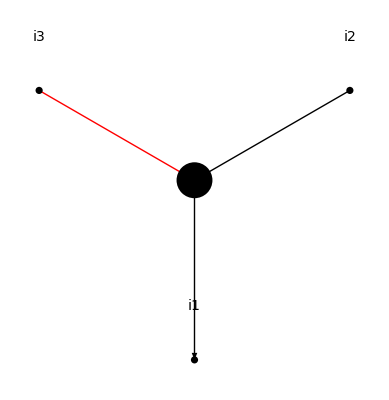
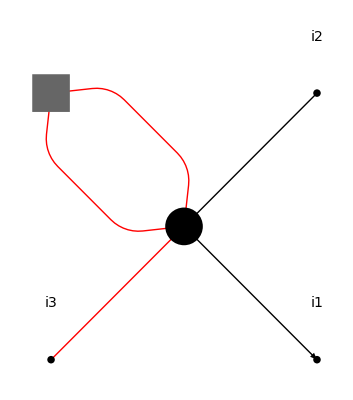
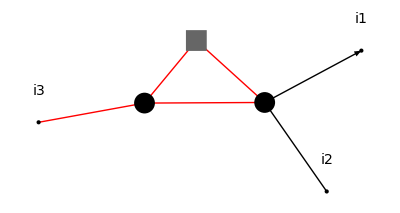
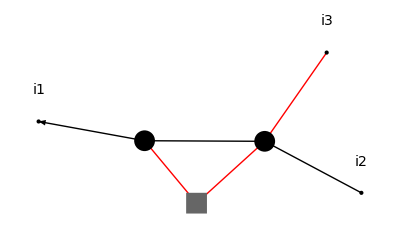
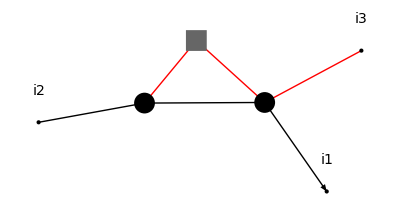
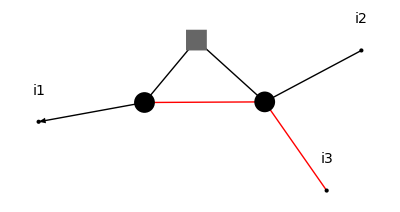
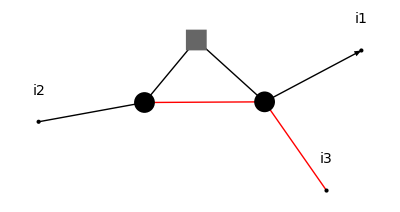
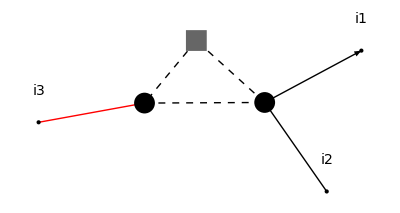
-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ |  |

```mathematica
RQCDquarkglue=doERGE[fieldsERGE,interactionsERGE,{Psib,Psi,A}]
RGEPlot[RQCDquarkglue,plotstyle]
```

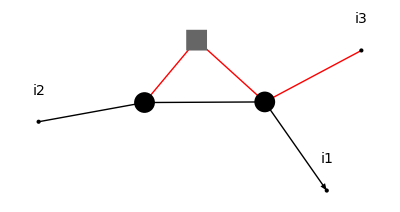
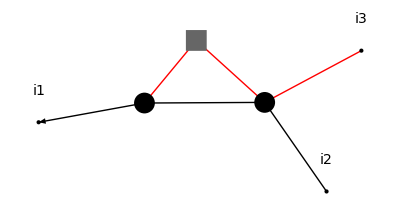
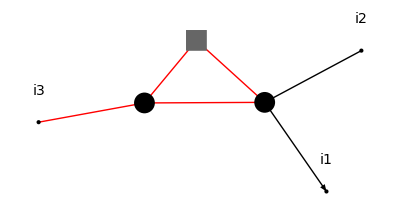
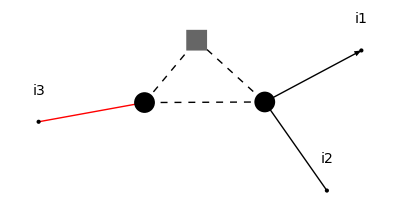
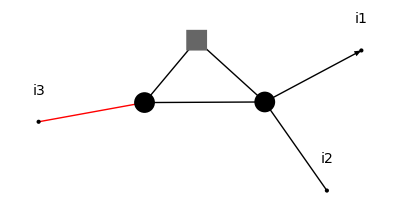
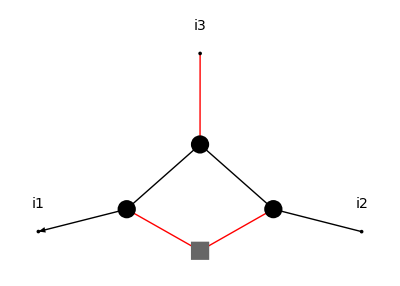
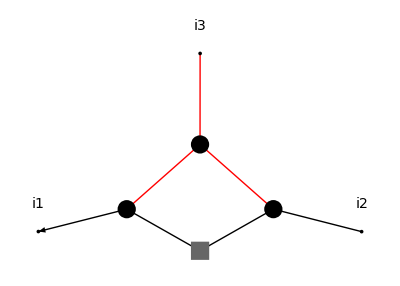
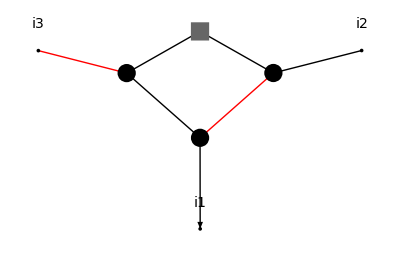
-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+2^ | -Graphics-+2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
RQCDquarkglueDoFun=doRGE[actionsymbolic,{{A,i3},{Psib,i1},{Psi,i2}}];
RGEPlot[RQCDquarkglueDoFun,plotstyle]
```

### Two-Quark-Two-Gluon

```mathematica
RQCDTwoquarkTwoglue=doERGE[fieldsERGE,interactionsERGE,{A,A,Psib,Psi}];
RGEPlot[RQCDTwoquarkTwoglue,plotstyle]
```

```mathematica
RQCDTwoquarkTwoglueDoFun=doRGE[actionsymbolic,{{A,i1},{A,i2},{Psib,i3},{Psi,i4}}];
RGEPlot[RQCDTwoquarkTwoglueDoFun,plotstyle]
```

### Pion Propagator

```mathematica
RQCDpionprop=doERGE[fieldsERGE,interactionsERGE,{pion,pion}];
RGEPlot[RQCDpionprop,plotstyle]
```

```mathematica
RQCDpionpropDoFun=doRGE[actionsymbolic,{{pion,i1},{pion,i2}}];
RGEPlot[RQCDpionpropDoFun,plotstyle]
```

### Pion Yukawa

```mathematica
RQCDYukawaPion=doERGE[fieldsERGE,interactionsERGE,{pion,Psib,Psi}];
RGEPlot[RQCDYukawaPion,plotstyle]
```

```mathematica
RQCDYukawaPionDoFun=doRGE[actionsymbolic,{{pion,i1},{Psib,i2},{Psi,i3}}];
RGEPlot[RQCDYukawaPionDoFun,plotstyle]
```